```mathematica
NS[]
```

```mathematica
ClearAll[xlogy];xlogy[x_,y_]:=If[x>0,x*Log[y],0];SetAttributes[xlogy,Listable];
```

```mathematica
rr=Range[-1,1];
```

```mathematica
(* parametric model in a three-outcome problem *)
pp[t_]={1,2,1}/{1+2*Exp[t]+Exp[2*t],Exp[-t]+2+Exp[t],Exp[-2*t]+2*Exp[-t]+1}
```

{1/(1+2 ⅇ^t+ⅇ^(2 t)),2/(2+ⅇ^-t+ⅇ^t),1/(1+ⅇ^(-2 t)+2 ⅇ^-t)}

```mathematica
pp[2]//N
```

{0.0142093,0.209987,0.775803}

```mathematica
SeedRandom[999];ndata=10^6;tdata=RandomChoice[pp[2]->rr,ndata];
```

```mathematica
tfreq=Table[(Count[tdata[[;;d]],#]&/@rr)/d,{d,1,ndata,Round[ndata/100]}];nfreq=Length@tfreq;td=Table[d,{d,1,ndata,Round[ndata/100]}];
```

```mathematica
tseqloglh=-Table[td[[d]]*Total[xlogy[tfreq[[d]],tfreq[[d]]/pp[2]]],{d,nfreq}];
```

```mathematica
seqloglh=-Table[td[[d]]*Total[xlogy[tfreq[[d]],tfreq[[d]]/pp[199/100]]],{d,nfreq}];
```

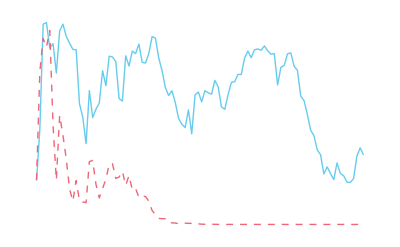

```mathematica
ListPlot[Exp@{tseqloglh,seqloglh},Joined->True,DataRange->td[[{1,-1}]]]
```

```mathematica
(* update hyperparameter from given data *)
updatepar[given_,k0_,mu0_,nu0_,s0_]:=Block[{k,mu,s,nu,ngiven=Length@T@given,mugiven,ncovgiven},
If[ngiven>0,

mugiven=Mean/@given;
ncovgiven=(given-Mean@T@given).T[given-Mean@T@given];
k=k0+ngiven;

{k,(k0*mu0+ngiven*mugiven)/k,nu0+ngiven,s0+ncovgiven+k0*ngiven*(T[{mugiven-mu0}].{mugiven-mu0})/k},

{k0,mu0,nu0,s0}]
];
```

```mathematica
(* posterior probability of want data conditional on given data *)
predpost[want_,given_,k0_,mu0_,nu0_,s0_]:=Block[{d=Length@want,k,mu,srow,scol,nu,nwant=Length[T@want]},

{k,mu,nu,srow}=updatepar[given,k0,mu0,nu0,s0];

scol=IdentityMatrix[nwant]+Table[1,nwant,nwant]/k;

PDF[MatrixTDistribution[T[Table[mu,nwant]],srow,scol,nu-d+1],want]
];
```

```mathematica
(* log-posterior *)
logpredpost[want_,given_,k0_,mu0_,nu0_,s0_]:=Block[{d=Length@want,k,mu,srow,scol,nu,nwant=Length[T@want]},

{k,mu,nu,srow}=updatepar[given,k0,mu0,nu0,s0];

scol=IdentityMatrix[nwant]+Table[1,nwant,nwant]/k;

LogLikelihood[MatrixTDistribution[T[Table[mu,nwant]],srow,scol,nu-d+1],{want}]
];
```

```mathematica
healthpost[datum_,given1_,given2_,k0_,mu0_,nu0_,s0_]:=Block[{d=Length@given1,k1,mu1,srow1,nu1,k2,mu2,srow2,nu2,p1,p2},
{k1,mu1,nu1,srow1}=updatepar[given1,k0,mu0,nu0,s0];
{k2,mu2,nu2,srow2}=updatepar[given2,k0,mu0,nu0,s0];

(*scol=IdentityMatrix[1]+Table[1,1,1]/k;*)

p1=PDF[MatrixTDistribution[T[Table[mu1,1]],srow1,IdentityMatrix[1]+Table[1,1,1]/k1,nu1-d+1],T@{datum}];
p2=PDF[MatrixTDistribution[T[Table[mu2,1]],srow2,IdentityMatrix[1]+Table[1,1,1]/k2,nu2-d+1],T@{datum}];
{p1,p2}/(p1+p2)
];
```

```mathematica
(* define the two data transformations and their Jacobians *)
ClearAll[tan,dtan];tan[x_]=Tan[Pi*x/2];SetAttributes[tan,Listable];
dtan[x_]=Pi/(1+Cos[Pi*x]);SetAttributes[dtan,Listable];
```

```mathematica
(* tan transform:
log-probability of dataset "want" given dataset "given" *)
ClearAll[tlogpredpost,tclogpredpost];tclogpredpost[want_,given_]:=Block[{d=Length@want},logpredpost[tan[want],tan[given],1,Table[0,d],d+1,(d+2)*IdentityMatrix[d]/4]+Total@Log@Flatten[dtan[want]]];

(* pre-data *)tlogpredpost[want_]:=Block[{d=Length@want},logpredpost[tan[want],Table[{},d],1,Table[0,d],d+1,(d+2)*IdentityMatrix[d]/4]+Total@Log@Flatten[dtan[want]]];
```

```mathematica
(* identity transform:
log-probability of dataset "want" given dataset "given" *)ClearAll[nlogpredpost,nclogpredpost];nclogpredpost[want_,given_]:=Block[{d=Length@want},logpredpost[want,given,1,Table[0,d],d+1,10*IdentityMatrix[d]]];

(* pre-data *)
nlogpredpost[want_]:=Block[{d=Length@want},logpredpost[want,Table[{},d],1,Table[0,d],d+1,10*IdentityMatrix[d]]];
```

```mathematica
Solve[tan[x]==y,x]
```

{{x→ConditionalExpression[(2 (ArcTan[y]+π C[1]))/π,C[1]∈ℤ]}}

```mathematica
SeedRandom[999];tdata=(2*ArcTan[#]/Pi)&@RandomVariate[NormalDistribution[1/2,2],10000];
```

```mathematica
dd=Length@{tan@tdata};updatepar[{tan@tdata},1,Table[0,dd],dd+1,(dd+2)*IdentityMatrix[dd]/4]
```

{10001,{0.522658},10002,{{39967.4}}}

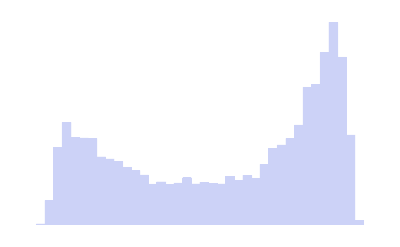

```mathematica
Histogram[tdata,50]
```

```mathematica
seqpost=Table[tlogpredpost[{tdata[[;;k]]}],{k,1,500,Round[500/10]}];
```

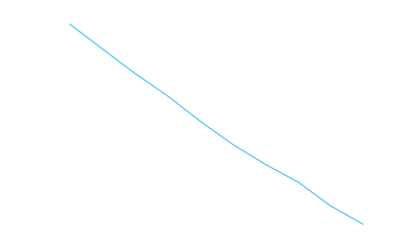

```mathematica
ListPlot[seqpost,Joined->True]
```

```mathematica
(* tests *)
```

```mathematica
testwant=RandomReal[{-5,5},{4,1}];
testgiven=RandomReal[{-5,5},{4,1}];
testk0=5;testmu0=RandomReal[{-5,5},4];
testnu0=20;
tests0=Block[{l=UpperTriangularize[RandomReal[{-5,5},{4,4}]]},T[l].l];
```

```mathematica
testgiven={{-2.2},{2.1},{3.4},{4.6}};
testk0=6;
testmu0={0.2, 3.7,-3.8,-3.6};
testnu0=21;
tests0=T@ArrayReshape[Range[16],{4,4}]
```

{{1,5,9,13},{2,6,10,14},{3,7,11,15},{4,8,12,16}}

```mathematica
MF/@updatepar[testgiven,testk0,testmu0,testnu0,tests0]
```

{7,(-0.142857
3.47143
-2.77143
-2.42857),22,(5.93714 | 8.29143 | -5.81143 | -3.86857
5.29143 | 8.19429 | 0.125714 | 2.75429
-11.8114 | -2.87429 | 55.4343 | 65.6057
-12.8686 | -3.24571 | 62.6057 | 73.6343)}

```mathematica
predpost[testwant,testgiven,testk0,testmu0,testnu0,tests0]
```

1.63909×10^-9

```mathematica
logpredpost[testwant,testgiven,testk0,testmu0,testnu0,tests0]
```

-20.2291

```mathematica
testgiven1=RandomReal[{-5,5},{4,1}];
testgiven2=RandomReal[{-5,5},{4,1}];
testdatum=RandomReal[{-5,5},4];
testk0=5;testmu0=RandomReal[{-5,5},4];
testnu0=20;
tests0=Block[{l=UpperTriangularize[RandomReal[{-5,5},{4,4}]]},T[l].l];
```

```mathematica
healthpost[testdatum,testgiven1,testgiven2,testk0,testmu0,testnu0,tests0]
```

{0.998847,0.0011528}

```mathematica
(* test formula *)
```

```mathematica
prob=predpost[testwant[[;;,{1}]],testgiven,testk0,testmu0,testnu0,tests0];

Do[
prob=prob*predpost[testwant[[;;,{i}]],T[Join[T@testgiven,T[testwant[[;;,;;(i-1)]]]]],testk0,testmu0,testnu0,tests0],
{i,2,Length[T@testwant]}]
```

```mathematica
prob
```

1.62964×10^-16

```mathematica
1-(prob/predpost[testwant,testgiven,testk0,testmu0,testnu0,tests0])
```

0.

```mathematica
prob2=predpost[T@Join[T@testwant,T@testgiven],Table[{},Length@testwant],testk0,testmu0,testnu0,tests0]/predpost[testgiven,Table[{},Length@testwant],testk0,testmu0,testnu0,tests0]
```

1.62964×10^-16

```mathematica
1-(prob2/predpost[testwant,testgiven,testk0,testmu0,testnu0,tests0])
```

6.99441×10^-15

```mathematica
(* apply to fMRI data *)
```

```mathematica
sdata=Import["..\\nanunana_fmri\\latest_code\\weights_Schizo_40cons"];Dimensions[sdata]
```

{40,49}

```mathematica
hdata=Import["..\\nanunana_fmri\\latest_code\\weights_con_40cons"];Dimensions[hdata]
```

{40,55}

```mathematica
ns=Length@T@sdata;nh=Length@T@hdata;
```

```mathematica
(* log-probability of each learning model: the id one has higher prob. *)MF[{tlogpredpost@#,nlogpredpost@#}&/@{sdata,hdata}]
```

(-980.982 | -1224.44
-877.26 | -1263.7)

```mathematica
Total@%
```

{-1858.24,-2488.14}

```mathematica
rg=Range[nd];MF[{{Mean@Table[tclogpredpost[sdata[[;;,{i}]],sdata[[;;,Delete[Range[Length@T@sdata],i]]]],{i,Length@T@sdata}],
Mean@Table[nclogpredpost[sdata[[;;,{i}]],sdata[[;;,Delete[Range[Length@T@sdata],i]]]],{i,Length@T@sdata}]},

{Mean@Table[tclogpredpost[hdata[[;;,{i}]],hdata[[;;,Delete[Range[Length@T@hdata],i]]]],{i,Length@T@hdata}],
Mean@Table[nclogpredpost[hdata[[;;,{i}]],hdata[[;;,Delete[Range[Length@T@hdata],i]]]],{i,Length@T@hdata}]}}]
```

(-19.8438 | -18.2458
-14.4001 | -15.9095)

```mathematica
Total[%]
```

{-34.2439,-34.1553}

```mathematica
(* probs for conditions given datum and previous data *)
nclogpred[datum_,hgiven_,sgiven_]:=
(#-Log@Total@Exp@#)&@{nclogpredpost[datum,hgiven],nclogpredpost[datum,sgiven]};


tclogpred[datum_,hgiven_,sgiven_]:=
(#-Log@Total@Exp@#)&@{tclogpredpost[datum,hgiven],tclogpredpost[datum,sgiven]};
```

```mathematica
jdata=T@Join[T@hdata,T@sdata];ntot=ns+nh;
jcond=Join[Table[1,nh],Table[2,ns]];
```

```mathematica
ClearAll[ifmri,tab];

tab=Table[
nev=nlogpredpost[hdata[[{ifmri}]]]+nlogpredpost[sdata[[{ifmri}]]];
tev=tlogpredpost[hdata[[{ifmri}]]]+tlogpredpost[sdata[[{ifmri}]]];
Prepend[means=Mean@Table[
arg0={{jdata[[ifmri,pat]]}};
arg1={Pick[Delete[jdata[[ifmri]],pat],Delete[jcond,pat],1]};
arg2={Pick[Delete[jdata[[ifmri]],pat],Delete[jcond,pat],2]};

nc1=nclogpred[arg0,{{}},{{}}][[jcond[[pat]]]];
nc2=nclogpred[arg0,arg1,arg2][[jcond[[pat]]]];
tc1=tclogpred[arg0,{{}},{{}}][[jcond[[pat]]]];
tc2=tclogpred[arg0,arg1,arg2][[jcond[[pat]]]];


{ifmri,
"diff: " ,tc2-nc2,
tev-nev,
"    id: ",
nev,
nc1,
nc2,
nc2-nc1,
"   tg: ",
tev,
tc1,
tc2,
tc2-tc1},{pat,ntot}],
Sign[means[[3]]*(tev-nev)]]
,{ifmri,40}];
```

```mathematica
MF@tab
```

(-1 | 1 | diff:  | -0.0401251 | 31.0871 |     id:  | -85.0999 | -0.693147 | -0.666534 | 0.0266131 |    tg:  | -54.0127 | -0.693147 | -0.706659 | -0.0135119
-1 | 2 | diff:  | -0.0314415 | 34.6395 |     id:  | -92.0765 | -0.693147 | -0.666536 | 0.0266107 |    tg:  | -57.437 | -0.693147 | -0.697978 | -0.00483075
-1 | 3 | diff:  | -0.0260436 | 28.124 |     id:  | -90.1204 | -0.693147 | -0.672278 | 0.0208688 |    tg:  | -61.9964 | -0.693147 | -0.698322 | -0.0051748
1 | 4 | diff:  | -0.221083 | -32.7416 |     id:  | -88.3387 | -0.693147 | -0.669922 | 0.0232253 |    tg:  | -121.08 | -0.693147 | -0.891005 | -0.197858
1 | 5 | diff:  | 0.0199146 | 38.6151 |     id:  | -86.5514 | -0.693147 | -0.633061 | 0.0600866 |    tg:  | -47.9363 | -0.693147 | -0.613146 | 0.0800012
1 | 6 | diff:  | 0.000778389 | 44.8575 |     id:  | -87.2673 | -0.693147 | -0.66668 | 0.0264672 |    tg:  | -42.4098 | -0.693147 | -0.665902 | 0.0272456
1 | 7 | diff:  | 0.0104004 | 44.5345 |     id:  | -88.3471 | -0.693147 | -0.673968 | 0.0191787 |    tg:  | -43.8126 | -0.693147 | -0.663568 | 0.0295791
-1 | 8 | diff:  | -0.0769117 | 5.35649 |     id:  | -89.8753 | -0.693147 | -0.67491 | 0.0182375 |    tg:  | -84.5188 | -0.693147 | -0.751821 | -0.0586743
1 | 9 | diff:  | 0.000194127 | 36.4996 |     id:  | -88.4711 | -0.693147 | -0.672196 | 0.0209516 |    tg:  | -51.9715 | -0.693147 | -0.672001 | 0.0211457
-1 | 10 | diff:  | -0.00140727 | 32.0532 |     id:  | -90.4793 | -0.693147 | -0.64347 | 0.0496773 |    tg:  | -58.4261 | -0.693147 | -0.644877 | 0.04827
-1 | 11 | diff:  | -0.00701747 | 40.7946 |     id:  | -83.1802 | -0.693147 | -0.662312 | 0.0308348 |    tg:  | -42.3856 | -0.693147 | -0.66933 | 0.0238173
-1 | 12 | diff:  | -0.062096 | 27.9234 |     id:  | -90.8053 | -0.693147 | -0.668976 | 0.0241716 |    tg:  | -62.8819 | -0.693147 | -0.731072 | -0.0379245
-1 | 13 | diff:  | -0.00483809 | 38.5721 |     id:  | -87.7049 | -0.693147 | -0.661522 | 0.0316248 |    tg:  | -49.1328 | -0.693147 | -0.666361 | 0.0267867
-1 | 14 | diff:  | -0.0694671 | 29.2923 |     id:  | -84.9806 | -0.693147 | -0.672849 | 0.020298 |    tg:  | -55.6883 | -0.693147 | -0.742316 | -0.0491691
-1 | 15 | diff:  | -0.0170696 | 21.058 |     id:  | -91.0698 | -0.693147 | -0.661221 | 0.0319258 |    tg:  | -70.0118 | -0.693147 | -0.678291 | 0.0148562
-1 | 16 | diff:  | -0.0142721 | 75.0443 |     id:  | -80.8595 | -0.693147 | -0.659812 | 0.0333352 |    tg:  | -5.81514 | -0.693147 | -0.674084 | 0.0190632
-1 | 17 | diff:  | -0.077702 | 6.75557 |     id:  | -92.0347 | -0.693147 | -0.673593 | 0.019554 |    tg:  | -85.2791 | -0.693147 | -0.751295 | -0.0581479
-1 | 18 | diff:  | -0.00136099 | 43.6073 |     id:  | -90.7313 | -0.693147 | -0.676449 | 0.0166985 |    tg:  | -47.124 | -0.693147 | -0.67781 | 0.0153376
-1 | 19 | diff:  | -0.0257668 | 22.5 |     id:  | -90.4607 | -0.693147 | -0.665602 | 0.0275451 |    tg:  | -67.9607 | -0.693147 | -0.691369 | 0.00177821
1 | 20 | diff:  | -0.295692 | -50.641 |     id:  | -88.6207 | -0.693147 | -0.667468 | 0.0256797 |    tg:  | -139.262 | -0.693147 | -0.96316 | -0.270013
1 | 21 | diff:  | -0.240696 | -41.7898 |     id:  | -89.8537 | -0.693147 | -0.665525 | 0.027622 |    tg:  | -131.644 | -0.693147 | -0.906221 | -0.213074
-1 | 22 | diff:  | -0.0554274 | 22.1682 |     id:  | -85.4279 | -0.693147 | -0.673112 | 0.0200347 |    tg:  | -63.2597 | -0.693147 | -0.72854 | -0.0353927
-1 | 23 | diff:  | -0.104124 | 15.4031 |     id:  | -86.9625 | -0.693147 | -0.659582 | 0.0335653 |    tg:  | -71.5595 | -0.693147 | -0.763706 | -0.0705586
-1 | 24 | diff:  | -0.0256551 | 28.4216 |     id:  | -87.0433 | -0.693147 | -0.659655 | 0.0334924 |    tg:  | -58.6216 | -0.693147 | -0.68531 | 0.00783731
-1 | 25 | diff:  | -0.0383386 | 14.5215 |     id:  | -92.2016 | -0.693147 | -0.675195 | 0.017952 |    tg:  | -77.6801 | -0.693147 | -0.713534 | -0.0203866
1 | 26 | diff:  | -0.274959 | -48.0184 |     id:  | -89.1506 | -0.693147 | -0.6747 | 0.0184475 |    tg:  | -137.169 | -0.693147 | -0.949658 | -0.256511
-1 | 27 | diff:  | -0.0226682 | 29.4307 |     id:  | -83.9815 | -0.693147 | -0.669091 | 0.0240563 |    tg:  | -54.5507 | -0.693147 | -0.691759 | 0.00138801
-1 | 28 | diff:  | -0.065459 | 33.2714 |     id:  | -82.877 | -0.693147 | -0.660629 | 0.0325187 |    tg:  | -49.6056 | -0.693147 | -0.726088 | -0.0329403
-1 | 29 | diff:  | -0.0350588 | 24.7571 |     id:  | -88.0253 | -0.693147 | -0.669922 | 0.0232247 |    tg:  | -63.2682 | -0.693147 | -0.704981 | -0.0118341
1 | 30 | diff:  | -0.343282 | -13.5523 |     id:  | -88.6347 | -0.693147 | -0.665265 | 0.0278823 |    tg:  | -102.187 | -0.693147 | -1.00855 | -0.315399
1 | 31 | diff:  | -0.127721 | -18.3954 |     id:  | -91.8554 | -0.693147 | -0.65595 | 0.0371973 |    tg:  | -110.251 | -0.693147 | -0.78367 | -0.0905232
1 | 32 | diff:  | -0.298914 | -54.0517 |     id:  | -90.2755 | -0.693147 | -0.673848 | 0.0192989 |    tg:  | -144.327 | -0.693147 | -0.972762 | -0.279615
-1 | 33 | diff:  | -0.0624457 | 32.5653 |     id:  | -86.0167 | -0.693147 | -0.666921 | 0.0262259 |    tg:  | -53.4513 | -0.693147 | -0.729367 | -0.0362198
1 | 34 | diff:  | -0.209188 | -35.6896 |     id:  | -88.9687 | -0.693147 | -0.669193 | 0.0239544 |    tg:  | -124.658 | -0.693147 | -0.878381 | -0.185233
-1 | 35 | diff:  | -0.0174382 | 42.5427 |     id:  | -81.9362 | -0.693147 | -0.661817 | 0.0313302 |    tg:  | -39.3935 | -0.693147 | -0.679255 | 0.0138921
-1 | 36 | diff:  | -0.0723918 | 26.0825 |     id:  | -91.2909 | -0.693147 | -0.666355 | 0.0267925 |    tg:  | -65.2085 | -0.693147 | -0.738746 | -0.0455993
-1 | 37 | diff:  | -0.0709503 | 20.4292 |     id:  | -89.1728 | -0.693147 | -0.660466 | 0.0326809 |    tg:  | -68.7436 | -0.693147 | -0.731417 | -0.0382694
1 | 38 | diff:  | -0.396358 | -56.7618 |     id:  | -86.1362 | -0.693147 | -0.669196 | 0.0239515 |    tg:  | -142.898 | -0.693147 | -1.06555 | -0.372406
-1 | 39 | diff:  | -0.0741294 | 11.2161 |     id:  | -87.5243 | -0.693147 | -0.66697 | 0.0261776 |    tg:  | -76.3082 | -0.693147 | -0.741099 | -0.0479518
-1 | 40 | diff:  | -0.0580807 | 16.7785 |     id:  | -92.3771 | -0.693147 | -0.669823 | 0.0233243 |    tg:  | -75.5986 | -0.693147 | -0.727904 | -0.0347564)

```mathematica
MF@tab[[Ordering[tab[[;;,4]]]]]
```

(1 | 38 | diff:  | -0.396358 | -56.7618 |     id:  | -86.1362 | -0.693147 | -0.669196 | 0.0239515 |    tg:  | -142.898 | -0.693147 | -1.06555 | -0.372406
1 | 30 | diff:  | -0.343282 | -13.5523 |     id:  | -88.6347 | -0.693147 | -0.665265 | 0.0278823 |    tg:  | -102.187 | -0.693147 | -1.00855 | -0.315399
1 | 32 | diff:  | -0.298914 | -54.0517 |     id:  | -90.2755 | -0.693147 | -0.673848 | 0.0192989 |    tg:  | -144.327 | -0.693147 | -0.972762 | -0.279615
1 | 20 | diff:  | -0.295692 | -50.641 |     id:  | -88.6207 | -0.693147 | -0.667468 | 0.0256797 |    tg:  | -139.262 | -0.693147 | -0.96316 | -0.270013
1 | 26 | diff:  | -0.274959 | -48.0184 |     id:  | -89.1506 | -0.693147 | -0.6747 | 0.0184475 |    tg:  | -137.169 | -0.693147 | -0.949658 | -0.256511
1 | 21 | diff:  | -0.240696 | -41.7898 |     id:  | -89.8537 | -0.693147 | -0.665525 | 0.027622 |    tg:  | -131.644 | -0.693147 | -0.906221 | -0.213074
1 | 4 | diff:  | -0.221083 | -32.7416 |     id:  | -88.3387 | -0.693147 | -0.669922 | 0.0232253 |    tg:  | -121.08 | -0.693147 | -0.891005 | -0.197858
1 | 34 | diff:  | -0.209188 | -35.6896 |     id:  | -88.9687 | -0.693147 | -0.669193 | 0.0239544 |    tg:  | -124.658 | -0.693147 | -0.878381 | -0.185233
1 | 31 | diff:  | -0.127721 | -18.3954 |     id:  | -91.8554 | -0.693147 | -0.65595 | 0.0371973 |    tg:  | -110.251 | -0.693147 | -0.78367 | -0.0905232
-1 | 23 | diff:  | -0.104124 | 15.4031 |     id:  | -86.9625 | -0.693147 | -0.659582 | 0.0335653 |    tg:  | -71.5595 | -0.693147 | -0.763706 | -0.0705586
-1 | 17 | diff:  | -0.077702 | 6.75557 |     id:  | -92.0347 | -0.693147 | -0.673593 | 0.019554 |    tg:  | -85.2791 | -0.693147 | -0.751295 | -0.0581479
-1 | 8 | diff:  | -0.0769117 | 5.35649 |     id:  | -89.8753 | -0.693147 | -0.67491 | 0.0182375 |    tg:  | -84.5188 | -0.693147 | -0.751821 | -0.0586743
-1 | 39 | diff:  | -0.0741294 | 11.2161 |     id:  | -87.5243 | -0.693147 | -0.66697 | 0.0261776 |    tg:  | -76.3082 | -0.693147 | -0.741099 | -0.0479518
-1 | 36 | diff:  | -0.0723918 | 26.0825 |     id:  | -91.2909 | -0.693147 | -0.666355 | 0.0267925 |    tg:  | -65.2085 | -0.693147 | -0.738746 | -0.0455993
-1 | 37 | diff:  | -0.0709503 | 20.4292 |     id:  | -89.1728 | -0.693147 | -0.660466 | 0.0326809 |    tg:  | -68.7436 | -0.693147 | -0.731417 | -0.0382694
-1 | 14 | diff:  | -0.0694671 | 29.2923 |     id:  | -84.9806 | -0.693147 | -0.672849 | 0.020298 |    tg:  | -55.6883 | -0.693147 | -0.742316 | -0.0491691
-1 | 28 | diff:  | -0.065459 | 33.2714 |     id:  | -82.877 | -0.693147 | -0.660629 | 0.0325187 |    tg:  | -49.6056 | -0.693147 | -0.726088 | -0.0329403
-1 | 33 | diff:  | -0.0624457 | 32.5653 |     id:  | -86.0167 | -0.693147 | -0.666921 | 0.0262259 |    tg:  | -53.4513 | -0.693147 | -0.729367 | -0.0362198
-1 | 12 | diff:  | -0.062096 | 27.9234 |     id:  | -90.8053 | -0.693147 | -0.668976 | 0.0241716 |    tg:  | -62.8819 | -0.693147 | -0.731072 | -0.0379245
-1 | 40 | diff:  | -0.0580807 | 16.7785 |     id:  | -92.3771 | -0.693147 | -0.669823 | 0.0233243 |    tg:  | -75.5986 | -0.693147 | -0.727904 | -0.0347564
-1 | 22 | diff:  | -0.0554274 | 22.1682 |     id:  | -85.4279 | -0.693147 | -0.673112 | 0.0200347 |    tg:  | -63.2597 | -0.693147 | -0.72854 | -0.0353927
-1 | 1 | diff:  | -0.0401251 | 31.0871 |     id:  | -85.0999 | -0.693147 | -0.666534 | 0.0266131 |    tg:  | -54.0127 | -0.693147 | -0.706659 | -0.0135119
-1 | 25 | diff:  | -0.0383386 | 14.5215 |     id:  | -92.2016 | -0.693147 | -0.675195 | 0.017952 |    tg:  | -77.6801 | -0.693147 | -0.713534 | -0.0203866
-1 | 29 | diff:  | -0.0350588 | 24.7571 |     id:  | -88.0253 | -0.693147 | -0.669922 | 0.0232247 |    tg:  | -63.2682 | -0.693147 | -0.704981 | -0.0118341
-1 | 2 | diff:  | -0.0314415 | 34.6395 |     id:  | -92.0765 | -0.693147 | -0.666536 | 0.0266107 |    tg:  | -57.437 | -0.693147 | -0.697978 | -0.00483075
-1 | 3 | diff:  | -0.0260436 | 28.124 |     id:  | -90.1204 | -0.693147 | -0.672278 | 0.0208688 |    tg:  | -61.9964 | -0.693147 | -0.698322 | -0.0051748
-1 | 19 | diff:  | -0.0257668 | 22.5 |     id:  | -90.4607 | -0.693147 | -0.665602 | 0.0275451 |    tg:  | -67.9607 | -0.693147 | -0.691369 | 0.00177821
-1 | 24 | diff:  | -0.0256551 | 28.4216 |     id:  | -87.0433 | -0.693147 | -0.659655 | 0.0334924 |    tg:  | -58.6216 | -0.693147 | -0.68531 | 0.00783731
-1 | 27 | diff:  | -0.0226682 | 29.4307 |     id:  | -83.9815 | -0.693147 | -0.669091 | 0.0240563 |    tg:  | -54.5507 | -0.693147 | -0.691759 | 0.00138801
-1 | 35 | diff:  | -0.0174382 | 42.5427 |     id:  | -81.9362 | -0.693147 | -0.661817 | 0.0313302 |    tg:  | -39.3935 | -0.693147 | -0.679255 | 0.0138921
-1 | 15 | diff:  | -0.0170696 | 21.058 |     id:  | -91.0698 | -0.693147 | -0.661221 | 0.0319258 |    tg:  | -70.0118 | -0.693147 | -0.678291 | 0.0148562
-1 | 16 | diff:  | -0.0142721 | 75.0443 |     id:  | -80.8595 | -0.693147 | -0.659812 | 0.0333352 |    tg:  | -5.81514 | -0.693147 | -0.674084 | 0.0190632
-1 | 11 | diff:  | -0.00701747 | 40.7946 |     id:  | -83.1802 | -0.693147 | -0.662312 | 0.0308348 |    tg:  | -42.3856 | -0.693147 | -0.66933 | 0.0238173
-1 | 13 | diff:  | -0.00483809 | 38.5721 |     id:  | -87.7049 | -0.693147 | -0.661522 | 0.0316248 |    tg:  | -49.1328 | -0.693147 | -0.666361 | 0.0267867
-1 | 10 | diff:  | -0.00140727 | 32.0532 |     id:  | -90.4793 | -0.693147 | -0.64347 | 0.0496773 |    tg:  | -58.4261 | -0.693147 | -0.644877 | 0.04827
-1 | 18 | diff:  | -0.00136099 | 43.6073 |     id:  | -90.7313 | -0.693147 | -0.676449 | 0.0166985 |    tg:  | -47.124 | -0.693147 | -0.67781 | 0.0153376
1 | 9 | diff:  | 0.000194127 | 36.4996 |     id:  | -88.4711 | -0.693147 | -0.672196 | 0.0209516 |    tg:  | -51.9715 | -0.693147 | -0.672001 | 0.0211457
1 | 6 | diff:  | 0.000778389 | 44.8575 |     id:  | -87.2673 | -0.693147 | -0.66668 | 0.0264672 |    tg:  | -42.4098 | -0.693147 | -0.665902 | 0.0272456
1 | 7 | diff:  | 0.0104004 | 44.5345 |     id:  | -88.3471 | -0.693147 | -0.673968 | 0.0191787 |    tg:  | -43.8126 | -0.693147 | -0.663568 | 0.0295791
1 | 5 | diff:  | 0.0199146 | 38.6151 |     id:  | -86.5514 | -0.693147 | -0.633061 | 0.0600866 |    tg:  | -47.9363 | -0.693147 | -0.613146 | 0.0800012)

```mathematica
Ordering[tab[[;;,4]]]
```

{38,30,32,20,26,21,4,34,31,23,17,8,39,36,37,14,28,33,12,40,22,1,25,29,2,3,19,24,27,35,15,16,11,13,10,18,9,6,7,5}

```mathematica
Ordering[tab[[;;,5]],40,Greater]
```

{16,6,7,18,35,11,5,13,9,2,28,33,10,1,27,14,24,3,12,36,29,19,22,15,37,40,23,25,39,17,8,30,31,4,34,21,26,20,32,38}

```mathematica
Ordering[tab[[;;,5]],40,Greater]
```

{5,10,31,23,24,16,37,28,15,13,35,11,30,21,19,36,1,2,6,33,39,20,12,27,34,38,40,4,29,9,3,14,22,17,32,7,26,8,25,18}

```mathematica
nperms=50;
Do[
RandomSeed[999];
lists=Mean@Table[perm=RandomSample[Range[ns+nh]];
permjdata=jdata[[ifmri,perm]];
permcond=jcond[[perm]];
Table[
arg1={{permjdata[[k+1]]}};
arg2={Pick[permjdata[[;;k]],permcond[[;;k]],1]};
arg3={Pick[permjdata[[;;k]],permcond[[;;k]],2]};

{nclogpred[arg1,arg2,arg3][[permcond[[k+1]]]],
tclogpred[arg1,arg2,arg3][[permcond[[k+1]]]]}
,{k,1,ntot-1}],nperms];

plot=ListPlot[T@lists,Joined->True,DataRange->{2,ntot},PlotRange->All,Epilog->Text[ifmri,Scaled[{0.05,0.95}]]];
expng["q"<>ToString[ifmri],plot]
,{ifmri,40}];
```

```mathematica
nperms=104;
fmri=23;
RandomSeed[999];
lists=Mean@Table[perm=RandomSample[Range[ns+nh]];
permjdata=jdata[[fmri,perm]];
permcond=jcond[[perm]];
Table[
arg1={{permjdata[[k+1]]}};
arg2={Pick[permjdata[[;;k]],permcond[[;;k]],1]};
arg3={Pick[permjdata[[;;k]],permcond[[;;k]],2]};

{nclogpred[arg1,arg2,arg3][[permcond[[k+1]]]],
tclogpred[arg1,arg2,arg3][[permcond[[k+1]]]]}
,{k,0,ntot-1}],nperms];
```

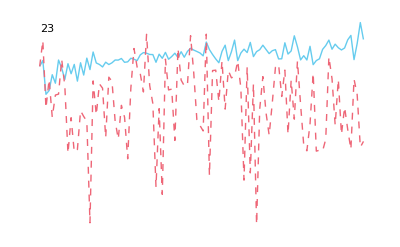

```mathematica
ListPlot[T@lists,Joined->True,DataRange->{1,ntot},PlotRange->{All,{Min@#,Max@#}&@lists},Epilog->Text[fmri,Scaled[{0.05,0.95}]]]
```

```mathematica
nperms=104;
fmri=36;
RandomSeed[999];
lists=Mean@Table[perm=RandomSample[Range[ns+nh]];
permjdata=jdata[[fmri,perm]];
permcond=jcond[[perm]];
Table[
arg1={{permjdata[[k+1]]}};
arg2={Pick[permjdata[[;;k]],permcond[[;;k]],1]};
arg3={Pick[permjdata[[;;k]],permcond[[;;k]],2]};

{nclogpred[arg1,arg2,arg3][[permcond[[k+1]]]],
tclogpred[arg1,arg2,arg3][[permcond[[k+1]]]]}
,{k,0,ntot-1}],nperms];
```

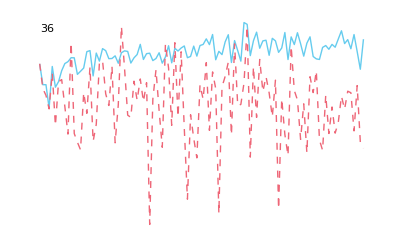

```mathematica
ListPlot[T@lists,Joined->True,DataRange->{1,ntot},PlotRange->{All,{Min@#,Max@#}&@lists},Epilog->Text[fmri,Scaled[{0.05,0.95}]]]
```

```mathematica
nperms=100;lists=Table[RandomSeed[999];Mean@Table[perm=RandomSample[Range[ns+nh]];
permjdata=jdata[[ifmri,perm]];
permcond=jcond[[perm]];
tclogpred[{{permjdata[[k+1]]}},
{Pick[permjdata[[;;k]],permcond[[;;k]],1]},
{Pick[permjdata[[;;k]],permcond[[;;k]],2]}][[permcond[[k+1]]]]
,nperms,{k,1,ntot-1}],{ifmri,3}];
```

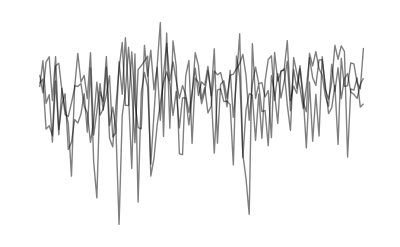

```mathematica
ListPlot[lists,Joined->True,PlotStyle->Directive[solid,Thin,Black,Opacity[0.5]]]
```

```mathematica
nperms=100;lists=Table[RandomSeed[999];Mean@Table[perm=RandomSample[Range[ns+nh]];
permjdata=jdata[[ifmri,perm]];
permcond=jcond[[perm]];
nclogpred[{{permjdata[[k+1]]}},
{Pick[permjdata[[;;k]],permcond[[;;k]],1]},
{Pick[permjdata[[;;k]],permcond[[;;k]],2]}][[permcond[[k+1]]]]
,nperms,{k,1,ntot-1}],{ifmri,3}];
```

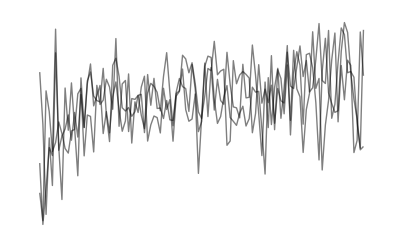

```mathematica
ListPlot[lists,Joined->True,PlotStyle->Directive[solid,Thin,Black,Opacity[0.5]]]
```

```mathematica
nclogpredpost[hdata[[{1},{1}]],hdata[[{1},2;;]]]
```

-1.80273

```mathematica
hdata[[1,1]]
```

-0.758649

```mathematica
hdata[[{1},{1}]]
```

{{-0.758649}}

```mathematica
Table[nclogpred[hdata[[{1},{k}]],hdata[[{1},;;]],sdata[[{1},;;]]],{k,Length@T@hdata}]
```

{{-0.388041,-1.1344},{-0.542437,-0.870672},{-0.588407,-0.810155},{-0.501947,-0.929758},{-0.608266,-0.785907},{-0.717426,-0.669444},{-0.84188,-0.563698},{-0.683554,-0.702833},{-0.570679,-0.832735},{-0.535404,-0.880521},{-0.772243,-0.619852},{-0.493675,-0.942581},{-0.625725,-0.765446},{-0.585733,-0.813503},{-0.79866,-0.597713},{-0.452068,-1.01146},{-0.506546,-0.922745},{-0.821171,-0.579669},{-0.679788,-0.706687},{-0.716622,-0.67021},{-0.486415,-0.954062},{-0.83345,-0.570129},{-0.586713,-0.812274},{-0.598666,-0.797495},{-0.762561,-0.62824},{-0.622793,-0.768828},{-0.605279,-0.789486},{-0.445485,-1.02308},{-0.921905,-0.5071},{-0.564451,-0.840887},{-0.673996,-0.712672},{-0.607026,-0.78739},{-0.621837,-0.769936},{-0.777251,-0.615571},{-0.755998,-0.634014},{-0.717136,-0.66972},{-0.843777,-0.562264},{-0.521847,-0.899983},{-0.733584,-0.654282},{-0.76357,-0.627359},{-0.718545,-0.668379},{-0.638053,-0.751455},{-0.736392,-0.651695},{-0.756275,-0.633769},{-0.621282,-0.77058},{-0.859999,-0.550195},{-0.67451,-0.712139},{-0.712376,-0.674281},{-0.49376,-0.942448},{-0.744923,-0.643921},{-0.754139,-0.635663},{-0.768628,-0.622966},{-0.614495,-0.778517},{-0.731451,-0.656257},{-0.893879,-0.526051}}

```mathematica
(* Check which components of the data lead to discrepancy between evidence and log-score *)
MF@Table[
cdata=hdata[[{k}]];nd=Length@T@cdata;rg=Range[nd];
{k,
m1=((tlogpredpost@#-nlogpredpost@#)/nd)&@cdata,

m2=Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]-
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]
},
{k,Length@hdata}]
```

(1 | 0.313065 | 0.0463278
2 | 0.299434 | 0.0638563
3 | 0.153698 | -0.115485
4 | 0.349637 | 0.0989031
5 | 0.285761 | 0.0175952
6 | 0.381567 | 0.140154
7 | 0.446173 | 0.196163
8 | 0.367114 | 0.127076
9 | 0.426503 | 0.177603
10 | 0.226332 | -0.0527461
11 | 0.437341 | 0.149573
12 | 0.187124 | -0.129024
13 | 0.444354 | 0.164336
14 | 0.336317 | 0.0251245
15 | 0.406713 | 0.160359
16 | 1.05393 | 0.751407
17 | -0.225569 | -0.504123
18 | 0.40885 | 0.183029
19 | 0.238591 | -0.00116054
20 | 0.409307 | 0.181447
21 | 0.452526 | 0.208111
22 | 0.218995 | -0.0529893
23 | 0.139024 | -0.226408
24 | 0.0849939 | -0.195043
25 | 0.38911 | 0.153436
26 | 0.390691 | 0.15782
27 | 0.0965329 | -0.216425
28 | 0.398289 | 0.0463138
29 | 0.238388 | -0.0296165
30 | 0.00670602 | -0.439913
31 | 0.401339 | 0.161818
32 | 0.400666 | 0.153827
33 | 0.354752 | 0.0458418
34 | 0.382651 | 0.124044
35 | 0.390728 | 0.0468544
36 | 0.175715 | -0.142263
37 | 0.176265 | -0.125646
38 | 0.358658 | 0.107236
39 | 0.40097 | 0.164326
40 | 0.226996 | -0.0547997)

```mathematica
cdata=hdata[[{12,23}]];nd=Length@T@cdata;rg=Range[nd];
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-68.0015,-87.4624}

```mathematica
Differences[%]
```

{-19.4609}

```mathematica
{tlogsc=Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
nlogsc=Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.39229,-1.02383}

```mathematica
Differences[%]
```

{0.368457}

```mathematica
tseqev=Table[tlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
nseqev=Table[nlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
```

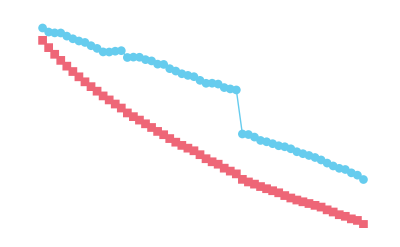

```mathematica
ListPlot[{tseqev,nseqev},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
tseqpred=Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];nseqpred=Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];
```

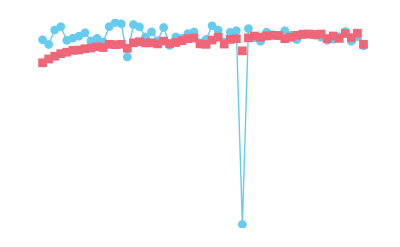

```mathematica
ListPlot[{tseqpred,nseqpred},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
nshuffle=100;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

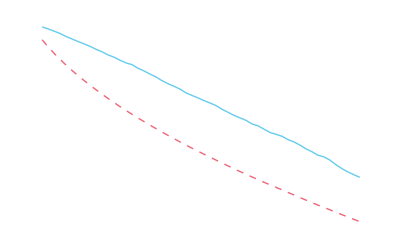
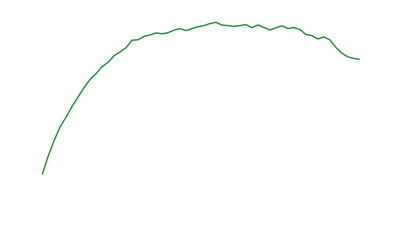

```mathematica
{ListPlot[{tmeanseqev,nmeanseqev},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5],ListPlot[tmeanseqev-nmeanseqev,Joined->True,PlotMarkers->None,PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5]}
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-68.0015,-87.4624}

```mathematica
nshuffle=500;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

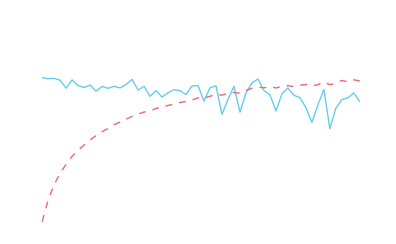
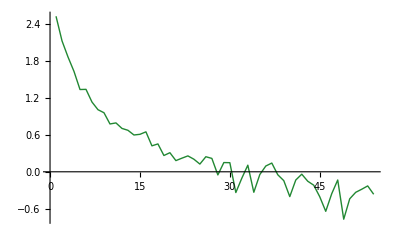

```mathematica
{ListPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5],
ListPlot[tmeanseqpred-nmeanseqpred,Joined->True,PlotMarkers->None,Axes->{True,False},PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5]}
```

```mathematica
{Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.39229,-1.02383}

```mathematica
(* Check which components of the data lead to discrepancy between evidence and log-score *)
MF@Table[
cdata=sdata[[{k}]];nd=Length@T@cdata;rg=Range[nd];
{k,(tlogpredpost@#-nlogpredpost@#)&@cdata,

Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]-
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]},
{k,Length@hdata}]
```

(1 | 13.8686 | -0.044937
2 | 18.1706 | 0.131994
3 | 19.6707 | 0.173272
4 | -51.9717 | -2.526
5 | 22.8983 | 0.202613
6 | 23.8713 | 0.22701
7 | 19.995 | 0.163372
8 | -14.8348 | -0.945361
9 | 13.042 | 0.000997891
10 | 19.605 | 0.172356
11 | 16.7408 | 0.0502144
12 | 17.6316 | 0.143352
13 | 14.1326 | 0.0638239
14 | 10.7949 | -0.141099
15 | -1.31122 | -0.294741
16 | 17.0779 | 0.114661
17 | 19.1619 | 0.178371
18 | 21.1205 | 0.182736
19 | 9.37748 | -0.0984317
20 | -73.1529 | -3.24316
21 | -66.6788 | -2.669
22 | 10.1235 | -0.108329
23 | 7.75674 | -0.14443
24 | 23.747 | 0.226104
25 | -6.87954 | -0.448856
26 | -69.5064 | -3.05982
27 | 24.1214 | 0.213228
28 | 11.3655 | -0.0302781
29 | 11.6457 | -0.0203288
30 | -13.9212 | -0.918875
31 | -40.469 | -1.6408
32 | -76.0883 | -3.0058
33 | 13.0539 | -0.0320591
34 | -56.7355 | -2.31038
35 | 21.0526 | 0.150756
36 | 16.4182 | 0.112116
37 | 10.7346 | -0.0135945
38 | -76.4879 | -3.01094
39 | -10.8373 | -0.749946
40 | 4.29374 | -0.232552)

```mathematica
cdata=sdata[[{14,40}]];nd=Length@T@cdata;rg=Range[nd];
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-62.9103,-85.5609}

```mathematica
Differences[%]
```

{-22.6506}

```mathematica
{tlogsc=Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
nlogsc=Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.37954,-1.20594}

```mathematica
Differences[%]
```

{0.1736}

```mathematica
tseqev=Table[tlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
nseqev=Table[nlogpredpost[cdata[[;;,;;i]]],{i,2,nd}];
```

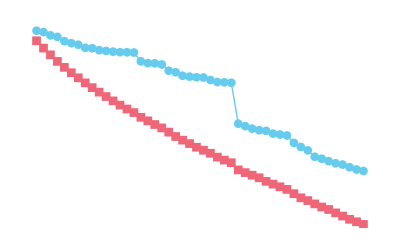

```mathematica
ListPlot[{tseqev,nseqev},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
tseqpred=Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];nseqpred=Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,;;(i-1)]]],{i,2,nd}];
```

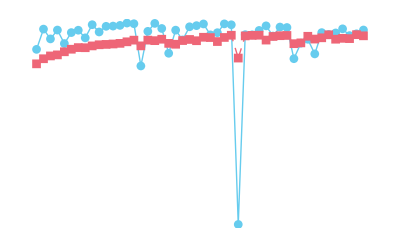

```mathematica
ListPlot[{tseqpred,nseqpred},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

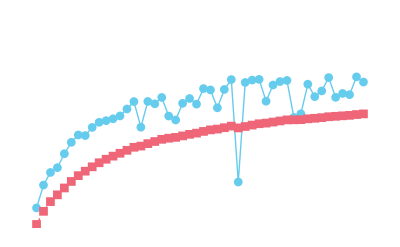

```mathematica
ListPlot[{nseqpred,nseqev/Range[2,nd]},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
nshuffle=100;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@Table[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle];
```

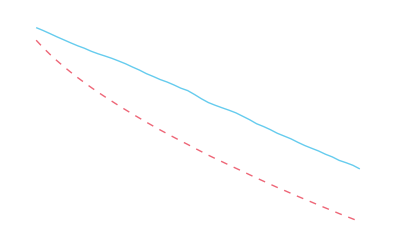
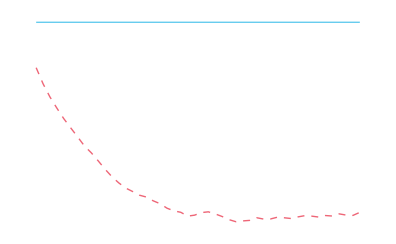
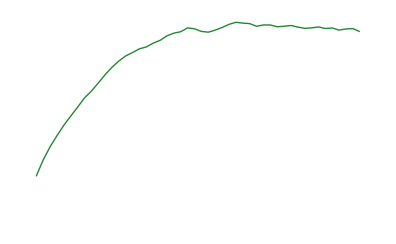

```mathematica
{ListPlot[{tmeanseqev,nmeanseqev},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size",Row[{ln," ", "p","(data|model)"}]},FrameStyle->Directive[FontSize->15]],

norm=Log[Exp@tmeanseqev+Exp@nmeanseqev];
ListPlot[{tmeanseqev-norm,nmeanseqev-norm},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size",Row[{ln," ", "p","(model|data)"}]},FrameStyle->Directive[FontSize->15]],ListPlot[tmeanseqev-nmeanseqev,Joined->True,PlotMarkers->None,PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size","difference"},FrameStyle->Directive[FontSize->15]]}
```

```mathematica
{tlogpredpost@#,nlogpredpost@#}&@cdata
```

{-62.9103,-85.5609}

```mathematica
nshuffle=500;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@Table[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle];
```

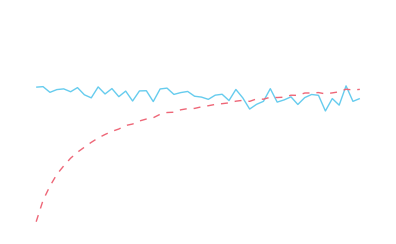
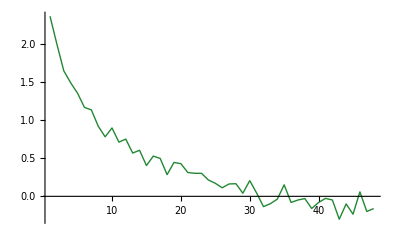

```mathematica
{ListPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size","leave-one-out"},FrameStyle->Directive[FontSize->15]],
ListPlot[tmeanseqpred-nmeanseqpred,Joined->True,PlotMarkers->None,Axes->{True,False},PlotStyle->green,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size","difference"},FrameStyle->Directive[FontSize->15]]}
```

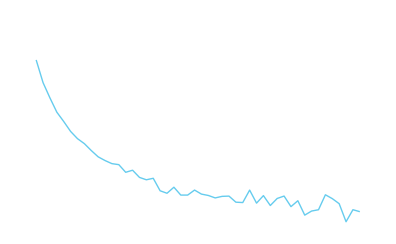

```mathematica
ListPlot[{1-nmeanseqev/Range[2,nd]/nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,All},ImageSize->a4shortside/1.5,FrameLabel->{"data size",""},FrameStyle->Directive[FontSize->15]]
```

```mathematica
{Mean@Table[tclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}],
Mean@Table[nclogpredpost[cdata[[;;,{i}]],cdata[[;;,Delete[rg,i]]]],{i,nd}]}
```

{-1.39229,-1.02383}

```mathematica
testdata2=T@Join[T@(hdata[[{1}]]),T@(sdata[[{1}]])];
```

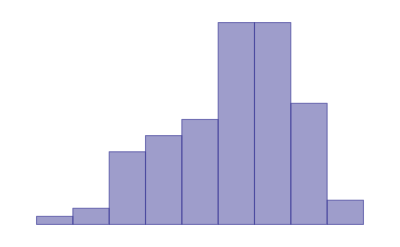

```mathematica
Histogram[testdata2,"Knuth",PDF,PlotRange->{All,All},ImageSize->a4shortside/2]
```

```mathematica
cdata=testdata2;nd=Length@T@cdata
```

104

```mathematica
nshuffle=200;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

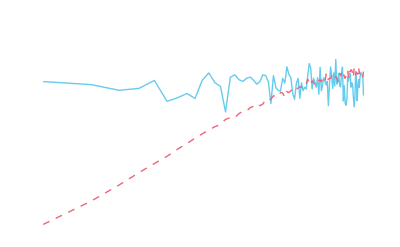

```mathematica
ListLogLinearPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,{All,All}}]
```

```mathematica
{tlogpredpost[cdata],nlogpredpost[cdata]}
```

{-57.9544,-68.4969}

```mathematica
nshuffle=5;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
norm=Log[Exp@tmeanseqev+Exp@nmeanseqev];
```

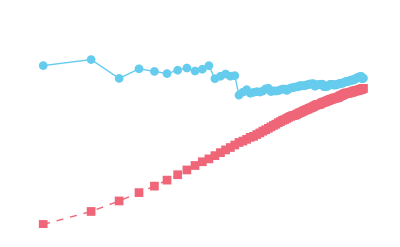

```mathematica
ListLogLinearPlot[{tmeanseqev/Range[2,nd],nmeanseqev/Range[2,nd]},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

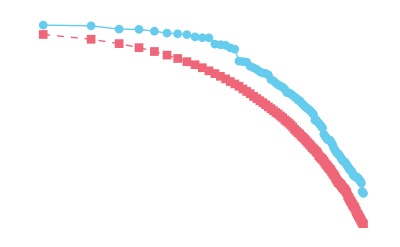

```mathematica
ListLogLinearPlot[{tmeanseqev,nmeanseqev},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

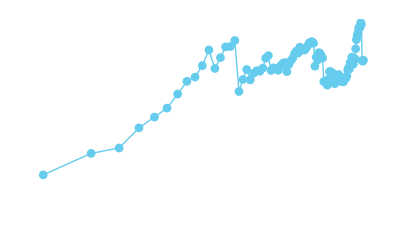

```mathematica
ListLogLinearPlot[tmeanseqev-nmeanseqev,Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
SeedRandom[999];testdata={RandomVariate[TruncatedDistribution[{-1,1},NormalDistribution[0,1/2]],1000]};
```

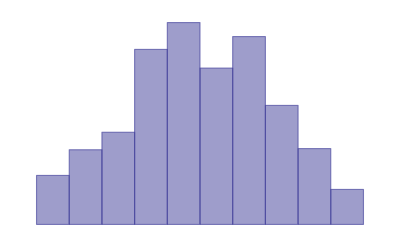

```mathematica
Histogram[testdata,"Knuth",PDF,PlotRange->{All,All},ImageSize->a4shortside/2]
```

```mathematica
cdata=testdata;nd=Length@T@cdata;
```

```mathematica
nshuffle=10;
```

```mathematica
SeedRandom[999];
tmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqpred=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nclogpredpost[cdata[[;;,{ord[[i]]}]],cdata[[;;,ord[[;;(i-1)]]]]],{i,2,nd}]
,nshuffle,Method->"CoarsestGrained"];
```

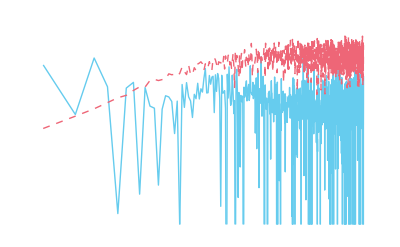

```mathematica
ListLogLinearPlot[{tmeanseqpred,nmeanseqpred},Joined->True,PlotMarkers->None,PlotRange->{All,{Auto,All}}]
```

```mathematica
nshuffle=2;
```

```mathematica
SeedRandom[999];
tmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[tlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,200}]
,nshuffle,Method->"CoarsestGrained"];
```

```mathematica
SeedRandom[999];
nmeanseqev=Mean@ParallelTable[ord=RandomSample[Range[nd]];
Table[nlogpredpost[cdata[[;;,ord[[;;i]]]]],{i,2,200}]
,nshuffle,Method->"CoarsestGrained"];
```

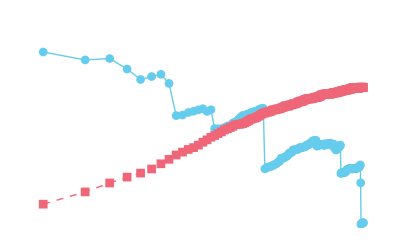

```mathematica
ListLogLinearPlot[{tmeanseqev/Range[2,200],nmeanseqev/Range[2,200]},Joined->True,PlotMarkers->Auto,PlotRange->{All,All}]
```

```mathematica
(* 23,40*)
cdata1=hdata[[{23}]];nd1=Length@T@cdata1;rg1=Range[nd1];
cdata2=sdata[[{23}]];nd2=Length@T@cdata2;rg2=Range[nd2];
```

```mathematica
ClearAll[tlogpredpost,tclogpredpost];tclogpredpost[want_,given_]:=Block[{d=Length@want},logpredpost[tan[want],tan[given],1,Table[0,d],d+1,(d+2)*IdentityMatrix[d]/4]+Total@Log@Flatten[dtan[want]]];

tlogpredpost[want_]:=Block[{d=Length@want},logpredpost[tan[want],Table[{},d],1,Table[0,d],d+1,(d+2)*IdentityMatrix[d]/4]+Total@Log@Flatten[dtan[want]]];
```

```mathematica
ClearAll[nlogpredpost,nclogpredpost];nclogpredpost[want_,given_]:=Block[{d=Length@want},logpredpost[want,given,1,Table[0,d],d+1,10*IdentityMatrix[d]]];

nlogpredpost[want_]:=Block[{d=Length@want},logpredpost[want,Table[{},d],1,Table[0,d],d+1,10*IdentityMatrix[d]]];
```

```mathematica
{Total@(tlogpredpost/@#),Total@(nlogpredpost/@#)}&@{sdata,hdata}
```

{-1858.24,-2488.14}

```mathematica
healthpost[datum_,given1_,given2_,k0_,mu0_,nu0_,s0_]:=Block[{d=Length@given1,k1,mu1,srow1,nu1,k2,mu2,srow2,nu2,p1,p2},
{k1,mu1,nu1,srow1}=updatepar[given1,k0,mu0,nu0,s0];
{k2,mu2,nu2,srow2}=updatepar[given2,k0,mu0,nu0,s0];

(*scol=IdentityMatrix[1]+Table[1,1,1]/k;*)

p1=PDF[MatrixTDistribution[T[Table[mu1,1]],srow1,IdentityMatrix[1]+Table[1,1,1]/k1,nu1-d+1],T@{datum}];
p2=PDF[MatrixTDistribution[T[Table[mu2,1]],srow2,IdentityMatrix[1]+Table[1,1,1]/k2,nu2-d+1],T@{datum}];
{p1,p2}/(p1+p2)
];
```